# PE: Numerical Simulations

## Synaptic activation

```mathematica
Integrate[HeavisideTheta[τ-(t-p)]/τ*DiracDelta[p-k],{p,-Infinity,t}]
```

ConditionalExpression[(HeavisideTheta[-k+t] HeavisideTheta[k-t+τ])/τ,k∈Reals&&t∈Reals]

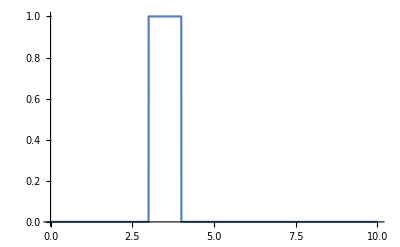

```mathematica
Plot[(HeavisideTheta[-k+t] HeavisideTheta[k-t+τ])/τ/.k->3/.τ->1,{t,0,10}]
```